1 - 10 Type and stability of critical point
Determine the type and stability of the critical point. Then find a real general solution and sketch or graph some of the trajectories in the phase plane.

I’m going to need to bring Tables 4.1

```mathematica
Grid[{{"Name","p=λ_1+λ_2","q=λ_1λ_2","Δ=(λ_1-λ_2)^2","Comments on λ_(1,) λ_2"},{"(a)Node","","q>0","Δ≥0","Real,same sign"},{"(b)Saddle point","","q<0","","Real,opposite signs"},{"(c)Center","p=0","q>0","","Pure imaginary"},{"(d)Spiral point","p≠0","","Δ<0","Complex, not pure imaginary"}},Frame->All]
```

Name | p=λ_1+λ_2 | q=λ_1λ_2 | Δ=(λ_1-λ_2)^2 | Comments on λ_(1,) λ_2
(a)Node |  | q>0 | Δ≥0 | Real,same sign
(b)Saddle point |  | q<0 |  | Real,opposite signs
(c)Center | p=0 | q>0 |  | Pure imaginary
(d)Spiral point | p≠0 |  | Δ<0 | Complex, not pure imaginary

and 4.2 in here for consultation.

```mathematica
Grid[{{"Type of Stability","p=λ_1+λ_2","q=λ_1λ_2"},{"(a)Stable and attractive","p<0","q>0"},{"(b)Stable","p≤0","q>0"},{"(c)Unstable","p>0 OR","OR q<0"}},Frame->All]
```

Type of Stability | p=λ_1+λ_2 | q=λ_1λ_2
(a)Stable and attractive | p<0 | q>0
(b)Stable | p≤0 | q>0
(c)Unstable | p>0 OR | OR q<0

1.  y_1'=y_1
y_2'=2 y_2

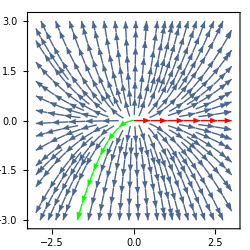

```mathematica
StreamPlot[{y1,2 y2},{y1,-3,3},{y2,-3,3},StreamPoints->{{{{1,0},Red},{{-1,-1},Green},Automatic}},ImageSize->250]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==y1[t],y2'[t]==2 y2[t]}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==y1[t],y2'[t]==2 y2[t]}

{{y1→Function[{t},ⅇ^t C[1]],y2→Function[{t},ⅇ^(2 t) C[2]]}}

1. Above: the general, real sol’ns.

```mathematica
te=e2[[1,1,2,2]]
```

ⅇ^t C[1]

The solution for y1, below, matches the text.

```mathematica
fe=te/.C[1]->c1
```

c1 ⅇ^t

```mathematica
e3=Eigensystem[{{1,0},{0,2}}]
```

{{2,1},{{0,1},{1,0}}}

```mathematica
Subscript[λ, 1]=2
```

2

```mathematica
Subscript[λ, 2]=1
```

1

```mathematica
p=Subscript[λ, 1]+Subscript[λ, 2]
```

3

```mathematica
q=Subscript[λ, 1] Subscript[λ, 2]
```

2

```mathematica
Δ=(Subscript[λ, 1]-Subscript[λ, 2])^2
```

1

1. Because p>0, the critical point is unstable according to Table 4-2.

```mathematica
TableForm[Table[{t,c1,fe},{t,4},{c1,-1,1}],TableHeadings->{{},{"t","c1 ","fe "}}]
```

| t | c1  | fe 
 | 1
-1
-ⅇ | 1
0
0 | 1
1
ⅇ
 | 2
-1
-ⅇ^2 | 2
0
0 | 2
1
ⅇ^2
 | 3
-1
-ⅇ^3 | 3
0
0 | 3
1
ⅇ^3
 | 4
-1
-ⅇ^4 | 4
0
0 | 4
1
ⅇ^4

```mathematica
fifo=Table[{t,fe},{t,4},{c1,-1,1}]
```

{{{1,-ⅇ},{1,0},{1,ⅇ}},{{2,-ⅇ^2},{2,0},{2,ⅇ^2}},{{3,-ⅇ^3},{3,0},{3,ⅇ^3}},{{4,-ⅇ^4},{4,0},{4,ⅇ^4}}}

```mathematica
hiu[c1_,t_]:=fe
```

```mathematica
plot1=Plot[Evaluate[Table[hiu[c1,t],{c1,-8,8}]],{t,-3,3},PlotRange->{-50,50},PlotStyle->Thickness[0.003]];
```

3. Above: This is a plot of the first sol’n, with trajectories of various constant values.

```mathematica
f[c1_,t_]:=c1 ⅇ^t
```

```mathematica
VectorPlot[{1,f[c1,t]},{c1,-3,3},{t,-1,1},Axes->True,Frame->False,VectorScale->{Tiny,Tiny,None},BaseStyle->AbsoluteThickness[0.4],PlotTheme->None,ImageSize->250];
```

```mathematica
plot2=VectorPlot[{1,f[t,c1]},{c1,-3,3},{t,-8,8},Axes->True,Frame->False,VectorScale->{Tiny,Tiny,None}, BaseStyle->AbsoluteThickness[0.4],PlotTheme->None,ImageSize->350];
```

```mathematica
Show[plot1,plot2];
```

```mathematica
fi=e2[[1,2,2,2]]
```

ⅇ^(2 t) C[2]

The solution for y2, below, agrees with the text.

```mathematica
fif=fi/.C[2]->c2
```

c2 ⅇ^(2 t)

```mathematica
fifi=Table[{t,fif},{t,4},{c2,-1,1}]
```

{{{1,-ⅇ^2},{1,0},{1,ⅇ^2}},{{2,-ⅇ^4},{2,0},{2,ⅇ^4}},{{3,-ⅇ^6},{3,0},{3,ⅇ^6}},{{4,-ⅇ^8},{4,0},{4,ⅇ^8}}}

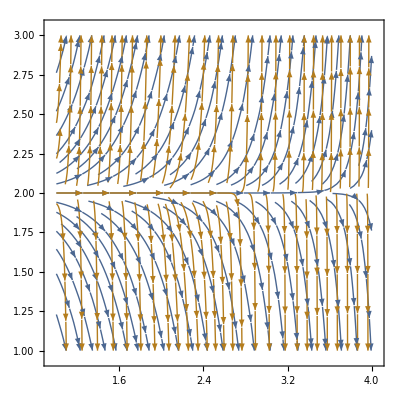

```mathematica
ListStreamPlot[{fifo,fifi}]
```

3.  y_1'=y_2
y_2'=-9 y_1

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==y2[t],y2'[t]==-9 y1[t]}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==y2[t],y2'[t]==-9 y1[t]}

{{y1→Function[{t},C[1] Cos[3 t]+1/3 C[2] Sin[3 t]],y2→Function[{t},C[2] Cos[3 t]-3 C[1] Sin[3 t]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

C[1] Cos[3 t]+1/3 C[2] Sin[3 t]

The solution for y_1, below, agrees with the text, provided that text constant A is assigned the value of C[1], and text constant B is assigned the value of 1/3C[2].

```mathematica
hiy[c1_,c2_,t_]:=c1 Cos[3 t]+1/3 c2 Sin[3 t]
```

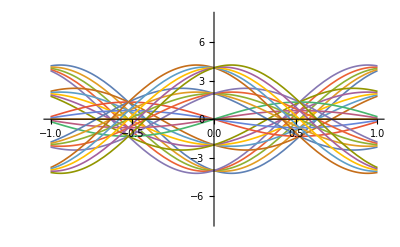

```mathematica
plot1=Plot[Evaluate[Table[hiy[c1,c2,t],{c1,-4,4,2},{c2,-4,4,2}]],{t,-1,1},PlotRange->{-8,8},PlotStyle->Thickness[0.003]]
```

1. Above: Some trajectories of the first sol’n. Below: the solution for y_2 agrees with the text, with appropriate constant assignments.

```mathematica
e4= e2[[1,2,2,2]]
```

C[2] Cos[3 t]-3 C[1] Sin[3 t]

```mathematica
hiz[c1_,c2_,t_]:=c2 Cos[3 t]-3 c1 Sin[3 t]
```

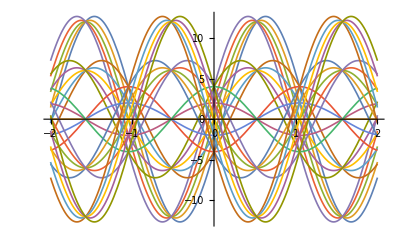

```mathematica
plot1=Plot[Evaluate[Table[hiz[c1,c2,t],{c1,-4,4,2},{c2,-4,4,2}]],{t,-2,2},PlotRange->Automatic,PlotStyle->Thickness[0.003]]
```

2. Above: Some trajectories of the second sol’n.

```mathematica
e5=Eigensystem[{{0,1},{-9,0}}]
```

{{3 ⅈ,-3 ⅈ},{{-ⅈ,3},{ⅈ,3}}}

```mathematica
p=3 ⅈ-3 ⅈ
```

0

```mathematica
q=3 ⅈ(-3 ⅈ)
```

9

```mathematica
Δ=(3 ⅈ-(-3 ⅈ))^2
```

-36

3. The system’s critical point is center. According to Table 4-2, it is stable.

```mathematica
e3p=e3/.{C[1]->1,C[2]->1}
```

Cos[3 t]+1/3 Sin[3 t]

```mathematica
e4p=e4/.{C[1]->1,C[2]->1}
```

Cos[3 t]-3 Sin[3 t]

```mathematica
ParametricPlot[{e3p,e4p},{t,-2,2},ImageSize->100,PlotStyle->Thickness[0.006]]
```

-Graphics-

5.  y_1'=-2 y_1+2 y_2
y_2'=-2 y_1-2 y_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==-2 y1[t]+2 y2[t],y2'[t]==-2 y1[t]-2 y2[t]}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==-2 y1[t]+2 y2[t],y2'[t]==-2 y1[t]-2 y2[t]}

{{y1→Function[{t},ⅇ^(-2 t) C[1] Cos[2 t]+ⅇ^(-2 t) C[2] Sin[2 t]],y2→Function[{t},ⅇ^(-2 t) C[2] Cos[2 t]-ⅇ^(-2 t) C[1] Sin[2 t]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

ⅇ^(-2 t) C[1] Cos[2 t]+ⅇ^(-2 t) C[2] Sin[2 t]

```mathematica
hiy[c1_,c2_,t_]:=ⅇ^(-2 t) c1 Cos[2 t]+ⅇ^(-2 t) c2 Sin[2 t]
```

Above: The green cell matches the answer in the text for y_1, assuming appropriate assignment of constants.

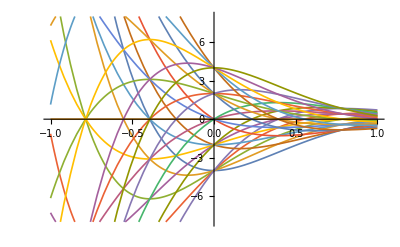

```mathematica
plot1=Plot[Evaluate[Table[hiy[c1,c2,t],{c1,-4,4,2},{c2,-4,4,2}]],{t,-1,1},PlotRange->{-8,8},PlotStyle->Thickness[0.003]]
```

```mathematica
e4=e2[[1,2,2,2]]
```

ⅇ^(-2 t) C[2] Cos[2 t]-ⅇ^(-2 t) C[1] Sin[2 t]

```mathematica
hiz[c1_,c2_,t_]:=ⅇ^(-2 t) c2 Cos[2 t]-ⅇ^(-2 t) c1 Sin[2 t]
```

Above: The green cell matches the answer in the text for y_2, assuming appropriate assignment of constants.

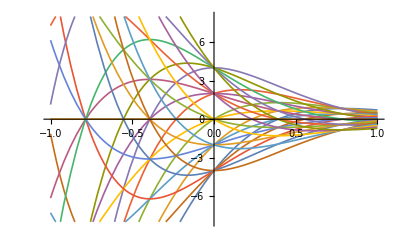

```mathematica
plot2=Plot[Evaluate[Table[hiz[c1,c2,t],{c1,-4,4,2},{c2,-4,4,2}]],{t,-1,1},PlotRange->{-8,8},PlotStyle->Thickness[0.003]]
```

```mathematica
e5=Eigensystem[{{-2,2},{-2,-2}}]
```

{{-2+2 ⅈ,-2-2 ⅈ},{{-ⅈ,1},{ⅈ,1}}}

```mathematica
p=-2+2 ⅈ+(-2-2 ⅈ)
```

-4

```mathematica
q=-2+2 ⅈ(-2-2 ⅈ)
```

2-4 ⅈ

```mathematica
Δ=((-2+2 ⅈ)-(-2-2 ⅈ))^2
```

-16

According to Table 4-1, the critical point is a spiral point. If the presence of imaginary part does not matter, the point is stable.

7.  y_1'=y_1+2 y_2
y_2'=2 y_1+y_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==y1[t]+2 y2[t],y2'[t]==2 y1[t]+y2[t]}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==y1[t]+2 y2[t],y2'[t]==2 y1[t]+y2[t]}

{{y1→Function[{t},1/2 ⅇ^-t (1+ⅇ^(4 t)) C[1]+1/2 ⅇ^-t (-1+ⅇ^(4 t)) C[2]],y2→Function[{t},1/2 ⅇ^-t (-1+ⅇ^(4 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(4 t)) C[2]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

1/2 ⅇ^-t (1+ⅇ^(4 t)) C[1]+1/2 ⅇ^-t (-1+ⅇ^(4 t)) C[2]

```mathematica
e5=Expand[e3]
```

1/2 ⅇ^-t C[1]+1/2 ⅇ^(3 t) C[1]-1/2 ⅇ^-t C[2]+1/2 ⅇ^(3 t) C[2]

```mathematica
e6=Collect[e5,ⅇ^(3 t)]
```

ⅇ^-t (C[1]/2-C[2]/2)+ⅇ^(3 t) (C[1]/2+C[2]/2)

```mathematica
e7=e6/.{(C[1]/2-C[2]/2)->c1,(C[1]/2+C[2]/2)->c2}
```

c1 ⅇ^-t+c2 ⅇ^(3 t)

Above: y1, matching the text answer.

```mathematica
Solve[(C[1]/2-C[2]/2)==c1&&(C[1]/2+C[2]/2)==c2,{c1,c2}]
```

{{c1→1/2 (C[1]-C[2]),c2→1/2 (C[1]+C[2])}}

```mathematica
hiy[c1_,c2_,t_]:=1/2 ⅇ^-t (1+ⅇ^(4 t)) c1+1/2 ⅇ^-t (-1+ⅇ^(4 t)) c2
```

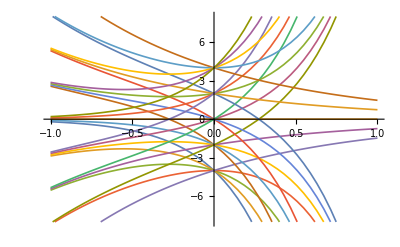

```mathematica
plot1=Plot[Evaluate[Table[hiy[c1,c2,t],{c1,-4,4,2},{c2,-4,4,2}]],{t,-1,1},PlotRange->{-8,8},PlotStyle->Thickness[0.003]]
```

```mathematica
e4=e2[[1,2,2,2]]
```

1/2 ⅇ^-t (-1+ⅇ^(4 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(4 t)) C[2]

```mathematica
e8=Expand[e4]
```

-1/2 ⅇ^-t C[1]+1/2 ⅇ^(3 t) C[1]+1/2 ⅇ^-t C[2]+1/2 ⅇ^(3 t) C[2]

```mathematica
e9=Collect[e8,ⅇ^(3 t)]
```

ⅇ^-t (-C[1]/2+C[2]/2)+ⅇ^(3 t) (C[1]/2+C[2]/2)

```mathematica
e10=e9/.{(-C[1]/2+C[2]/2)->-c1,(C[1]/2+C[2]/2)->c2}
```

-c1 ⅇ^-t+c2 ⅇ^(3 t)

Above: y2, matching the text answer.

```mathematica
Solve[(-C[1]/2+C[2]/2)==-c1&&(C[1]/2+C[2]/2)==c2,{c1,c2}]
```

{{c1→1/2 (C[1]-C[2]),c2→1/2 (C[1]+C[2])}}

The system of constants used in this problem is consistent with the text’s, as demonstrated in pink cells.

```mathematica
hiz[c1_,c2_,t_]:=1/2 ⅇ^-t (-1+ⅇ^(4 t)) c1+1/2 ⅇ^-t (1+ⅇ^(4 t)) c2
```

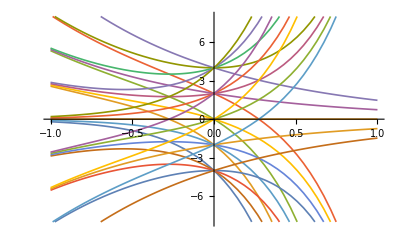

```mathematica
plot2=Plot[Evaluate[Table[hiz[c1,c2,t],{c1,-4,4,2},{c2,-4,4,2}]],{t,-1,1},PlotRange->{-8,8},PlotStyle->Thickness[0.003]]
```

```mathematica
Eigensystem[{{1,2},{2,1}}]
```

{{3,-1},{{1,1},{-1,1}}}

```mathematica
p=3-1
```

2

```mathematica
q=3(-1)
```

-3

```mathematica
Δ=(3-(-1))^2
```

16

According to Table 4-1, the critical point is a saddle point. According to Table 4-2, it is unstable.

9. y_1'=4 y_1+y_2
y_2'=4 y_1+4 y_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==4 y1[t]+y2[t],y2'[t]==4 y1[t]+4 y2[t]}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==4 y1[t]+y2[t],y2'[t]==4 y1[t]+4 y2[t]}

{{y1→Function[{t},1/2 ⅇ^(2 t) (1+ⅇ^(4 t)) C[1]+1/4 ⅇ^(2 t) (-1+ⅇ^(4 t)) C[2]],y2→Function[{t},ⅇ^(2 t) (-1+ⅇ^(4 t)) C[1]+1/2 ⅇ^(2 t) (1+ⅇ^(4 t)) C[2]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

1/2 ⅇ^(2 t) (1+ⅇ^(4 t)) C[1]+1/4 ⅇ^(2 t) (-1+ⅇ^(4 t)) C[2]

```mathematica
e4=Expand[e3]
```

1/2 ⅇ^(2 t) C[1]+1/2 ⅇ^(6 t) C[1]-1/4 ⅇ^(2 t) C[2]+1/4 ⅇ^(6 t) C[2]

```mathematica
e5=Collect[e4,ⅇ^(6 t)]
```

ⅇ^(2 t) (C[1]/2-C[2]/4)+ⅇ^(6 t) (C[1]/2+C[2]/4)

```mathematica
e6=e5/.{(C[1]/2-C[2]/4)->c2,(C[1]/2+C[2]/4)->c1}
```

c2 ⅇ^(2 t)+c1 ⅇ^(6 t)

Above: the text answer for y_1.

```mathematica
Solve[(C[1]/2-C[2]/4)==c2&&(C[1]/2+C[2]/4)==c1,{c1,c2}]
```

{{c1→1/4 (2 C[1]+C[2]),c2→1/4 (2 C[1]-C[2])}}

```mathematica
e7[c1_,c2_,t_]:=c2 ⅇ^(2 t)+c1 ⅇ^(6 t)
```

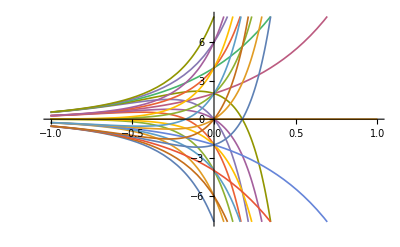

```mathematica
plot1=Plot[Evaluate[Table[e7[c1,c2,t],{c1,-4,4,2},{c2,-4,4,2}]],{t,-1,1},PlotRange->{-8,8},PlotStyle->Thickness[0.003]]
```

```mathematica
e8=e2[[1,2,2,2]]
```

ⅇ^(2 t) (-1+ⅇ^(4 t)) C[1]+1/2 ⅇ^(2 t) (1+ⅇ^(4 t)) C[2]

```mathematica
e9=Expand[e8]
```

-ⅇ^(2 t) C[1]+ⅇ^(6 t) C[1]+1/2 ⅇ^(2 t) C[2]+1/2 ⅇ^(6 t) C[2]

```mathematica
e10=Collect[e9,ⅇ^(6 t)]
```

ⅇ^(2 t) (-C[1]+C[2]/2)+ⅇ^(6 t) (C[1]+C[2]/2)

```mathematica
e11=e10/.{(-C[1]+C[2]/2)->-2 c2,(C[1]+C[2]/2)->2 c1}
```

-2 c2 ⅇ^(2 t)+2 c1 ⅇ^(6 t)

Above: the text answer for y_2.

```mathematica
Solve[(-C[1]+C[2]/2)==-2 c2&&(C[1]+C[2]/2)==2 c1,{c1,c2}]
```

{{c1→1/4 (2 C[1]+C[2]),c2→1/4 (2 C[1]-C[2])}}

```mathematica
Eigensystem[{{4,1},{4,4}}]
```

{{6,2},{{1,2},{-1,2}}}

```mathematica
p=6+2
```

8

```mathematica
q=6 2
```

12

```mathematica
Δ=(6-2)^2
```

16

According to Table 4.1, the critical point is a node. According to Table 4.2, it is unstable.

11 - 18 Trajectories of systems and second-order ODEs. Critical points.

11. Damped oscillations. Solve y''+2y'+2y=0. What kind of curves are the trajectories?

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn=y''[x]+2y'[x]+2y[x]==0
```

2 y[x]+2 y'[x]+y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},ⅇ^-x C[2] Cos[x]+ⅇ^-x C[1] Sin[x]]}}

The above green cell matches the answer in the text.

```mathematica
eqn/.sol//Simplify
```

{True}

In order to find the eigensystem, I need to make this equation into a system, using numbered lines (9) and (10) on p. 135. So I will have y_1=y, and y_2=y', and y_3=y'' . And the arrangement will be adopted whereby y_1'=y_2, and y_2'=y_3. Going by the text examples, the rows of the system matrix will be formed of the coefficients of the equations (lhs) of y_1' and y_2'. This will be

y_1'=y_2 | by definition
y''=y_3=y_2'=-2 y_1-2 y_2 | by problem equation description

What are the critical points? From the first expression, the first coordinate will be zero. From the second expression, the  coordinates will be equal. This means that {0,0} will be the only critical point.

```mathematica
A=({{0, 1}, {-2, -2}})
```

{{0,1},{-2,-2}}

```mathematica
{vals,vecs}=Eigensystem[A]
```

{{-1+ⅈ,-1-ⅈ},{{-1-ⅈ,2},{-1+ⅈ,2}}}

```mathematica
p=vals[[1]]+vals[[2]]
```

-2

```mathematica
q=vals[[1]]*vals[[2]]
```

2

```mathematica
Δ=(vals[[1]]-vals[[2]])^2
```

-4

According to Table 4.1, the critical point is a spiral point, and according to Table 4.2 it is stable.

17. Perturbation. The system in example 4 in section 4.3, p. 144, has a center as its critical point. Replace each a_jk in example 4 by a_jk + b. Find values of b such that you get (a) a saddle point, (b) a stable and attractive node, (c) a stable and attractive spiral, (d) an unstable spiral, (e) an unstable node.

```mathematica
ClearAll["Global`*"]
```

The characteristic matrix for this problem, given in the example, is like this, (but without the added ‘b’ characters).

```mathematica
y'=({{0+b, 1+b}, {-4+b, 0+b}})
```

{{b,1+b},{-4+b,b}}

```mathematica
beig=Table[Eigenvalues[y'],{b,{-π,-ⅇ,-2,-1.5,-1,-0.3,0.1,3,π,4}}];
```

```mathematica
Table[{{beig[[n,1]]+beig[[n,2]]},{beig[[n,1]]*beig[[n,2]]},{(beig[[n,1]]-beig[[n,2]])^2}},{n,1,10}];
```

```mathematica
g2=Grid[N[Table[{n-6,beig[[n,1]]+beig[[n,2]],beig[[n,1]]*beig[[n,2]],(beig[[n,1]]-beig[[n,2]])^2},{n,1,10}]],Frame->All];
```

```mathematica
g1=Grid[{{" n ","     p      ","      q     ","      Δ       "}},Frame->All];
```

```mathematica
Column[{g1,g2}]
```

n  |      p       |       q      |       Δ       
-5. | -6.28319 | -5.42478 | 61.1775
-4. | -5.43656 | -4.15485 | 46.1756
-3. | -4. | -2. | 24.
-2. | -3. | -0.5 | 11.
-1. | -2. | 1. | 0.
0. | -0.6+0. ⅈ | 3.1+0. ⅈ | -12.04+0. ⅈ
1. | 0.2+0. ⅈ | 4.3+0. ⅈ | -17.16+0. ⅈ
2. | 6. | 13. | -16.
3. | 6.28319+0. ⅈ | 13.4248+0. ⅈ | -14.2207+0. ⅈ
4. | 8. | 16. | 0.

The grid below identifies the ‘n’ number critical points with the required characteristics, based on Table 4.1 and 4.2.

```mathematica
g3=Grid[{{-3,"unstable saddle point"},{-1,"stable and attrac node"},{0,"stable and attrac spiral"},{2,"unstable spiral"},{4,"unstable node"}},Frame->All]
```

-3 | unstable saddle point
-1 | stable and attrac node
0 | stable and attrac spiral
2 | unstable spiral
4 | unstable node